# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

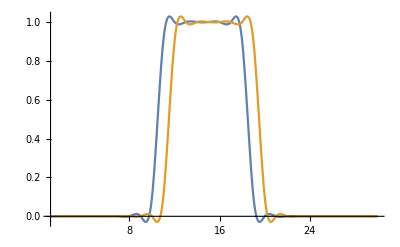

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}]
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=1*dfline1'[p1];
fric2=1*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<n,Return[{v1,v2,"oksign",e+1}],Return[{0.,0.,"sign",e}]]];

(* magnitud *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<n,Return[{v1,v2,"okmag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

If[e<=n,{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.01,"converged","ok"],e},Return[{0.,0.,status,e}]]

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,n_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.5,3,"ok",0.};
i=0;
p=11;
```

```mathematica
n=4;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,1,noteBookMode]
```

{0.330509,0.18458,ok,0.}

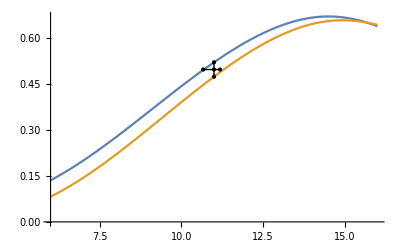

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)
(*n=allowed failed levels, u= shift on v solution through levels*)

newValues[i_,n_,u_,{v1_,v2_,status_,e_},newv0_,"ConstrainedNewMethod"]:=Block[{v,r,rs,newVals},(
v=v1+v2;

If[e>n,
Return[{{0.,0.}}];
];

If[v≠0. && status=="ok",
newVals=Table[
r=RandomReal[];
{r,1-r}*v
,{j,i}];
If[u≠0.,Join[newVals,newVals-u, newVals+u],newVals]

,
newv0
]

)]
```

```mathematica
(* We create the list of values in case v=0 *)
r=RandomReal[];
rangev0=Range[0,5,0.2];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0]
```

{{0.,0.},{0.170182,0.0298178},{0.340364,0.0596356},{0.510547,0.0894534},{0.680729,0.119271},{0.850911,0.149089},{1.02109,0.178907},{1.19128,0.208725},{1.36146,0.238542},{1.53164,0.26836},{1.70182,0.298178},{1.872,0.327996},{2.04219,0.357814},{2.21237,0.387631},{2.38255,0.417449},{2.55273,0.447267},{2.72292,0.477085},{2.8931,0.506903},{3.06328,0.53672},{3.23346,0.566538},{3.40364,0.596356},{3.57383,0.626174},{3.74401,0.655992},{3.91419,0.685809},{4.08437,0.715627},{4.25455,0.745445},{0.,0.},{0.0298178,0.170182},{0.0596356,0.340364},{0.0894534,0.510547},{0.119271,0.680729},{0.149089,0.850911},{0.178907,1.02109},{0.208725,1.19128},{0.238542,1.36146},{0.26836,1.53164},{0.298178,1.70182},{0.327996,1.872},{0.357814,2.04219},{0.387631,2.21237},{0.417449,2.38255},{0.447267,2.55273},{0.477085,2.72292},{0.506903,2.8931},{0.53672,3.06328},{0.566538,3.23346},{0.596356,3.40364},{0.626174,3.57383},{0.655992,3.74401},{0.685809,3.91419},{0.715627,4.08437},{0.745445,4.25455},{0.,0.},{0.2,0.},{0.4,0.},{0.6,0.},{0.8,0.},{1.,0.},{1.2,0.},{1.4,0.},{1.6,0.},{1.8,0.},{2.,0.},{2.2,0.},{2.4,0.},{2.6,0.},{2.8,0.},{3.,0.},{3.2,0.},{3.4,0.},{3.6,0.},{3.8,0.},{4.,0.},{4.2,0.},{4.4,0.},{4.6,0.},{4.8,0.},{5.,0.},{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.},{0.,1.2},{0.,1.4},{0.,1.6},{0.,1.8},{0.,2.},{0.,2.2},{0.,2.4},{0.,2.6},{0.,2.8},{0.,3.},{0.,3.2},{0.,3.4},{0.,3.6},{0.,3.8},{0.,4.},{0.,4.2},{0.,4.4},{0.,4.6},{0.,4.8},{0.,5.}}

```mathematica
nV=newValues[10,1,0.25,{-1,-1.,"ok",1.},newv0,"ConstrainedNewMethod"]
Total/@nV
```

{{-1.11432,-0.885679},{-1.79765,-0.202347},{-1.26239,-0.737609},{-0.816583,-1.18342},{-0.678207,-1.32179},{-1.44338,-0.556624},{-0.42456,-1.57544},{-1.91704,-0.0829606},{-0.958084,-1.04192},{-1.99328,-0.00672246},{-1.36432,-1.13568},{-2.04765,-0.452347},{-1.51239,-0.987609},{-1.06658,-1.43342},{-0.928207,-1.57179},{-1.69338,-0.806624},{-0.67456,-1.82544},{-2.16704,-0.332961},{-1.20808,-1.29192},{-2.24328,-0.256722},{-0.864321,-0.635679},{-1.54765,0.0476526},{-1.01239,-0.487609},{-0.566583,-0.933417},{-0.428207,-1.07179},{-1.19338,-0.306624},{-0.17456,-1.32544},{-1.66704,0.167039},{-0.708084,-0.791916},{-1.74328,0.243278}}

{-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5}

```mathematica
(* This will give back a value that converged or is on "ok" status. If not, error is returned and {v1,v2} goes back to 0. *)

pickNewValue[tableNewVals_,condition_,"ConstrainedNewMethod"]:=Block[{newValOk,newValCon,newValAny,noFakeConverge},(

(* Criterias to select a solution *)
newValCon=Select[tableNewVals,(#[[3]]=="converged")&&condition[#]&,1];
newValAny=Select[tableNewVals,(#[[3]]≠ "ok"&&#[[3]]≠ "oksign"&&#[[3]]≠ "okmag"&&#[[3]]≠ "converged")&&condition[#]&,1];
newValOk=Select[tableNewVals,(#[[3]]=="ok"||#[[3]]=="oksign"||#[[3]]=="okmag")&& condition[#]&,1];

noFakeConverge=Select[tableNewVals,(#[[3]]≠ "ok"&&#[[3]]≠ "oksign"&&#[[3]]≠ "okmag"&&#[[3]]≠ "converged")&,1];

(* No solution meets criteria *)
If[newValCon=={}&&newValAny=={}&&newValOk=={},

If[noFakeConverge=={},
Flatten[{0.,0.,"fakeconverged",tableNewVals[[1,4]]+1}]
,
Flatten[{0.,0.,noFakeConverge[[1,3]],noFakeConverge[[1,4]]}]
]

,
(* solution meets criteria but it did not converge *)
If[newValCon=={},
(* solution meets criteria but isn't ok or converged *)
If[newValOk=={},
newValAny[[1]]
,

Flatten[{newValOk[[1,1;;2]],"ok",newValOk[[1,4]]}]
],

newValCon[[1]]
]

]
)]
```

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<1;
```

```mathematica
threshold=0.001;
n=1;
p0=13;
i=10;

updateValues={0.,0.,"ok",0.};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)

nV=newValues[10,1,0.02,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNV=Table[
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),1,noteBookMode]

,{j,1,i}];

tValues
,{v,nV}];

sol=pickNewValue[tableNV,condition,"ConstrainedNewMethod"]
```

{0.97598,0.00931544,converged,0.}

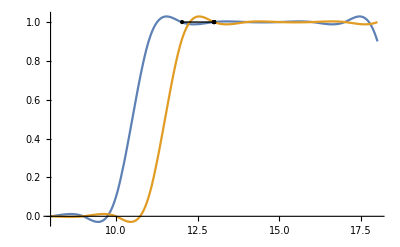

```mathematica
(* see *)
seePlot[p0,5,sol[[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, allowed failed levels, shift on v solution through levels, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_,n_,u_, p0_,listv0_,condition_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c, updateValues,nV,tableNewValues,tValues},(

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Do[


(* Flag to stop when e≥n *)
If[updateValues[[4]]<=n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],updateValues[[4]]}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,n,u,updateValues[[1;;4]],listv0,"ConstrainedNewMethod"];
(* compute at this scale, using current motion estimate *)

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];

Do[
tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),n,"ConstrainedNewMethod"];
If[tValues[[3]]!="ok",Break[]];

,{j,1,i}];

tValues
,{v,nV}];

(* We only update updateValues with the tValue that converged *)
updateValues=pickNewValue[tableNewValues,condition,"ConstrainedNewMethod"];


c=c-1;
,{f,1,Length[pyrfunctions]}];

updateValues[[1;;3]]
)];
```

#### Test

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<1;
```

```mathematica
p=14;
```

{{0.,0.,sign,1},{0.,0.,sign,2},{0.,0.,sign,3},{0.,0.,mag,4},{0.,0.,sign,5},{0.,0.,mag,6},{0.,0.,sign,7},{0.,0.,sign,8},{0.977152,0.0177972,converged,9},{0.0904403,0.868147,converged,10},{0.499975,0.500004,converged,11},{0.873387,0.0820325,converged,12},{0.0181978,0.981802,converged,13},{0.000351183,0.987291,converged,14},{0.,0.,sign,15},{0.988337,0.0116628,converged,16},{0.0155932,0.972449,converged,17},{0.116776,0.87429,converged,18},{0.499983,0.499996,converged,19},{0.876731,0.123269,converged,20},{0.0173524,0.982648,converged,21},{0.00721631,0.977101,converged,22},{0.,0.,sign,23},{0.,0.,sign,24},{0.,0.,mag,25},{0.,0.,sign,26},{0.,0.,sign,27},{0.,0.,sign,28},{0.,0.,sign,29},{0.,0.,mag,30}}

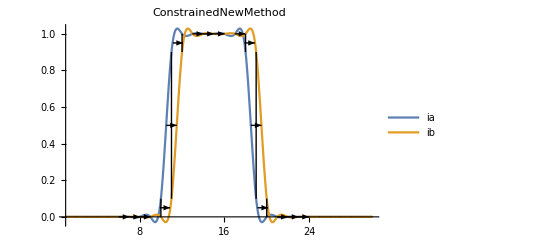

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[1,0.02,newv0,condition,Range[1,30],pyrf12[[1;;2]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[0,0.02,newv0,condition,Range[1,30],pyrf12[[1;;2]],0.001,noteBookMode]
```

#### Test

{{0.00810541,0.970426,converged,9},{0.108971,0.870266,converged,10},{0.499883,0.500002,converged,11},{0.867796,0.0953481,converged,12},{0.00161228,0.975142,converged,13},{0.0013227,0.984313,converged,14},{0.,0.,sign,15},{0.984313,0.0013227,converged,16},{0.983934,0.0148601,converged,17},{0.0894419,0.872174,converged,18},{0.499891,0.499994,converged,19}}

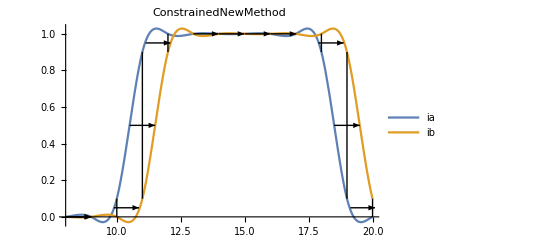

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[0,0.1,newv0,condition,Range[p-5,p+5],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[0,0.1,newv0,condition,Range[p-6,p+6],pyrf12[[1;;4]],0.001,noteBookMode]
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
{v1, v2,status,e}={0.5,3,"ok",0.};

i=40;
p=15;

(* m-> max lvl, n-> min lvl *)
m=2;
n=2;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i,1,0.02 ,p,{{0.5,3}},pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

{0.,0.,okmag}

{0.,okmag}

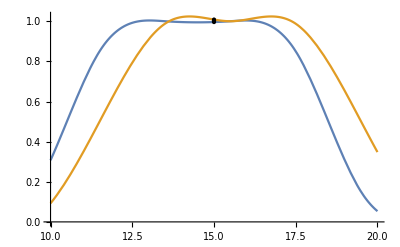

```mathematica
(* see *)
seePlot[p,5,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

{{0.,0.,sign,1},{0.,0.,sign,2},{0.,0.,mag,3},{0.,0.,mag,4},{0.,0.,mag,5},{0.,0.,mag,6},{0.,0.,sign,7},{0.0150841,0.976695,converged,8},{0.975858,0.00720443,converged,9},{0.11607,0.870133,converged,10},{0.499956,0.499814,converged,11},{0.910431,0.0757231,converged,12},{0.0119177,0.981661,converged,13},{0.00233714,0.985297,converged,14},{0.,0.,ok,15},{0.0213985,0.976227,converged,16},{0.00127736,0.966065,converged,17},{0.0902067,0.871438,converged,18},{0.499965,0.499806,converged,19},{0.887665,0.112335,converged,20},{0.980619,0.0193807,converged,21},{0.00252557,0.973776,converged,22},{0.,0.,sign,23},{0.,0.,mag,24},{0.,0.,sign,25},{0.,0.,sign,26},{0.,0.,mag,27},{0.,0.,sign,28},{0.,0.,mag,29},{0.,0.,mag,30}}

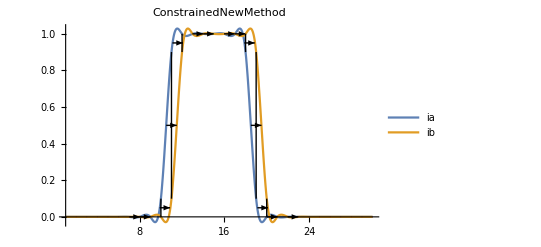

```mathematica
r=RandomReal[];
rangev0=Range[-5,5,0.5];

newv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0];

tes1=lineTest[1,0.02,newv0,condition,Range[1,Length[line1]],pyrf12[[1;;4]],0.001,noteBookMode]

(* This function is called from pyramidalCyclope1D *)
seeAllLine[1,0.02,newv0,condition,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

## Graphics for One pixel

```mathematica
pickNewValueIter[tableIterNewVals_,"ConstrainedNewMethod"]:=Block[{newIterValCon,newIterValAny,newIterValOk,noIterFakeConverge},(
newIterValCon=Select[tableIterNewVals,(Last[#][[3]]=="converged"&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
newIterValAny=Select[tableIterNewVals,((Last[#][[3]]≠ "ok" ||Last[#][[3]]≠ "oksign"||Last[#][[3]]≠ "okmag"||Last[#][[3]]≠ "converged")&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
newIterValOk=Select[tableIterNewVals,((Last[#][[3]]=="ok" ||Last[#][[3]]=="oksign"||Last[#][[3]]=="okmag")&&Last[#][[1]]*Last[#][[2]]>0 && 0<Last[#][[2]]+Last[#][[1]]<1)&,1];
noIterFakeConverge=Select[tableIterNewVals,(Last[#][[3]]≠ "ok" ||Last[#][[3]]≠ "oksign"||Last[#][[3]]≠ "okmag"||Last[#][[3]]≠ "converged")&,1];

(* No solution meets criteria *)
If[newIterValCon=={}&&newIterValAny=={}&&newIterValOk=={},

If[noIterFakeConverge=={},
(* If any kind of ok does not meet the criteria, there is no solution in this lvl*)
Join[tableIterNewVals[[1]],{Flatten[{0.,0.,"fakeconverge",Last[tableIterNewVals[[1]]][[4]]+1}]}]
,
Join[noIterFakeConverge[[1]],{Flatten[{0.,0.,Last[noIterFakeConverge[[1]]][[3]],Last[noIterFakeConverge[[1]]][[4]]}]}]
]

,
(* solution meets criteria but it did not converge *)
If[newIterValCon=={},
(* solution meets criteria but isn't ok or converged *)
If[newIterValOk=={},
newIterValAny[[1]]
,
Join[newIterValOk[[1]],{Flatten[{Last[newIterValOk[[1]]][[1;;2]],"ok",Last[newIterValOk[[1]]][[4]]}]}]
],
newIterValCon[[1]]
]
]

)]
```

```mathematica
PyrFlow1DIter[10,1,0.02,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
```

{0.,0.,ok}

```mathematica
i=10;
p0=1;
threshold=0.001;
n=1;
updateValues={0.,0.,"ok",0.};
```

```mathematica
(* Flag to stop when e≥2 *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 5 and -5 *)
nV=newValues[10,1,0.02,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];

tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0,  pyrf12[[n]],threshold*2^(-n+1),1,"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"][[All,1;;3]]

Last[goodValIter]
```

{{-3.33518,-1.66482,okmag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag}}

{0.,0.,mag}

```mathematica
goodValIter
```

{{-3.33518,-1.66482,okmag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag}}

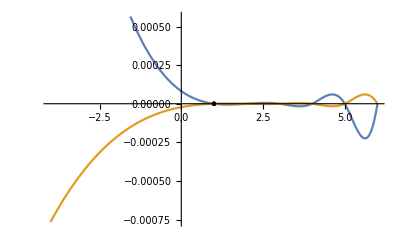

```mathematica
(* see *)
seePlot[p0,5,Last[goodValIter][[1;;2]],pyrf12[[n]]]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, allowed failed levels, shift on v solution through levels, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_,n_,u_, p0_,newv0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,tValues,iterTable,goodValIter,nV},(


c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0.};

Table[

(* Flag to stop when e≥n *)
If[updateValues[[4]]<=n,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],updateValues[[4]]}];

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, list newv0 is created and fed to the function to try all it's contained values *)
nV=newValues[10,n,u,updateValues[[1;;4]],newv0,"ConstrainedNewMethod"];


tableNewValues=Table[

(* We initialize whith values calculated at nV and last calculated updateValues[[3;;4]]*)
tValues=Flatten[{v,updateValues[[3;;4]]}];


iterTable=Table[

tValues=PyrUpgrade1D[tValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),n,"ConstrainedNewMethod"]
,{j,1,i}]

,{v,nV}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues,"ConstrainedNewMethod"];
updateValues=Last[goodValIter];

goodValIter[[All,1;;3]]
,{f,1,Length[pyrfunctions]}]

)];
```

#### Test

```mathematica
Table[
PyrFlow1D[10,1,0.04,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]
,{p,1,30}]
```

{{0.,0.,mag},{0.,0.,sign},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,converged},{0.,0.,ok},{0.,0.,sign},{0.,0.,sign},{0.,0.,sign},{0.,0.,oksign},{0.,0.,sign},{0.,0.,sign},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,sign},{0.,0.,mag},{0.,0.,sign}}

```mathematica
Table[
PyrFlow1DIter[10,1,0.04,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{{0.,0.,mag},{0.,0.,sign},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.989126,4.4394×10^-16,converged},{0.995507,0.00101624,converged},{0.102752,0.884291,converged},{0.,0.,sign},{0.876693,0.0833938,converged},{0.00310637,0.996894,converged},{0.00171363,0.998286,converged},{0.,0.,ok},{0.998286,0.00171363,converged},{0.0179254,0.974985,converged},{0.109694,0.878952,converged},{0.,0.,sign},{0.882694,0.117306,converged},{0.974916,0.025084,ok},{6.16583×10^-18,0.989126,converged},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,mag},{0.,0.,sign},{0.,0.,mag},{0.,0.,sign}}

```mathematica
Table[
PyrFlow1D[10,1,0.02, p,newv0, pyrf12[[1;;4]],0.001,noteBookMode]==PyrFlow1DIter[10,1,0.02,p,newv0, pyrf12[[1;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{True,True,True,True,True,True,True,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True}

#### Test

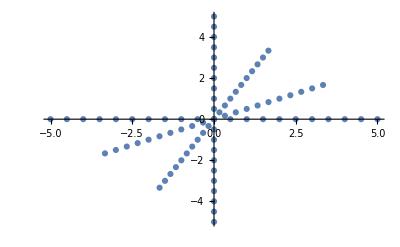

```mathematica
(* List of initial values we are going to try *)
ListPlot[newv0]
```

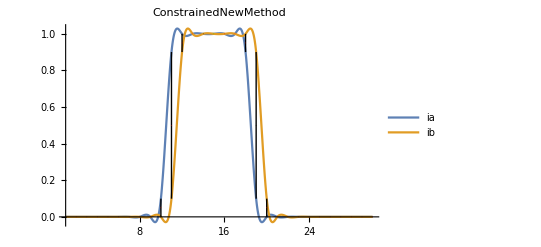

```mathematica
seeAllLine[1,0.04,newv0,Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

```mathematica
(* Creating list of initial Values *)
rangev0=Range[0,5,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

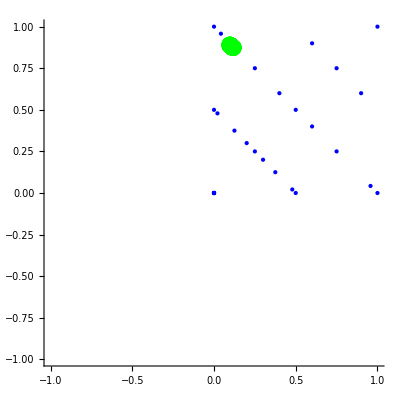
-Graphics-ConstrainedNewMethod

```mathematica
lvlmin=1;
lvlmax=3;
p=10;
dis=4;

mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,1,0.04,p,listv0,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";

(*pixelInitialValueGraphics[10,1000,p,{-10,10},dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]*)
```